Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

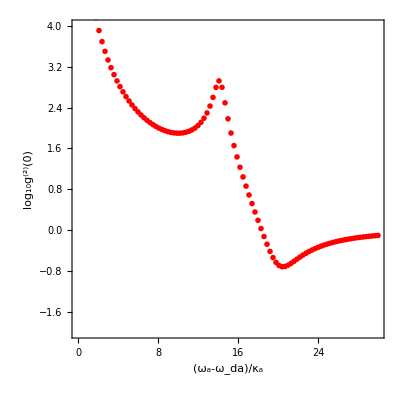

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=8*2*Pi;
ωge=8*2*Pi;


g=0.01*ωr;
γeg=0.1*g;
κ=0.1*g;

F=1.5*κ;
max1=30*κ;
min1=0;      (*max and min value of Δ*)
segment1=100;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
Na=4;
C1=√((4*F^2*Δ^2)/(8*F^4+4 (Na*g^2-Δ^2)^2+8*F^2*(Na*g^2+Δ^2)+Δ^2 κ^2));


equs=Table[{Δ*ToExpression[StringJoin["Ce1",ToString[i]]]+C2*√2*g-I/2*κ*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce1",ToString[i]]]+F*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce1",ToString[i]]]==0,g*C1+F*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce0",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,2*Δ*C2+F*C1*√2-I*κ*C2+g*(Sum[ToExpression[StringJoin["Ce1",ToString[i]]],{i,Na}])*√2==0];


vars={C2,Table[ToExpression[StringJoin["Ce1",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["Ce0",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
Ce1data=Table[ToExpression[StringJoin["Ce1",ToString[i]]]/.S[[1,i+1]],{i,1,Na}];

logg20=Chop[Log10[2/(C1*Conjugate[C1])*(C2data/C1)*(Conjugate[C2data]/Conjugate[C1])]];


{Δ/κ,logg20},{m,1,100+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_a-ω_da)/κ_a","log_10g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->False,PlotStyle->{Red},Frame->True,PlotMarkers->"OpenMarkers",PlotRange->{{0,30},{-2,4}},AspectRatio->1]
```

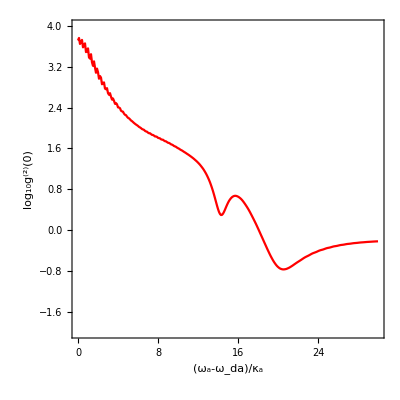

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];
(*定义基本量*)
n=6;(*定义光场展开数*)
columnlengthcavity=n;
columnlengthatom=16;(*原子基矢数*)
columnlengthf=columnlengthcavity*columnlengthatom;
columncut=7;
matrixvariablef=columncut*columncut;(*ρf的变元数*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
σr={{0,1},{0,0}};
σl={{0,0},{1,0}};
unity2={{1,0},{0,1}};
unityatom=IdentityMatrix[columnlengthatom];
unitycavity=IdentityMatrix[n];
(*定义光子数空间在基矢0，1，2,3,4,5下算符的矩阵表示*)
a={{0,1,0,0,0,0},{0,0,√2,0,0,0},{0,0,0,√3,0,0},{0,0,0,0,2,0},{0,0,0,0,0,√5},{0,0,0,0,0,0}};
adaige={{0,0,0,0,0,0},{1,0,0,0,0,0},{0,√2,0,0,0,0},{0,0,√3,0,0,0},{0,0,0,2,0,0},{0,0,0,0,√5,0}};
(*定义全空间ee0,eg0,ge0,gg0,gg1,ee2,eg2,ge2,gg2算符的矩阵表示，变量名都加f表示*)
af=KroneckerProduct[a,unityatom];
adaigef=KroneckerProduct[adaige,unityatom];
σx1f=KroneckerProduct[unitycavity,σx,unity2,unity2,unity2];
σz1f=KroneckerProduct[unitycavity,σz,unity2,unity2,unity2];
σr1f=KroneckerProduct[unitycavity,σr,unity2,unity2,unity2];
σl1f=KroneckerProduct[unitycavity,σl,unity2,unity2,unity2];
σx2f=KroneckerProduct[unitycavity,unity2,σx,unity2,unity2];
σz2f=KroneckerProduct[unitycavity,unity2,σz,unity2,unity2];
σr2f=KroneckerProduct[unitycavity,unity2,σr,unity2,unity2];
σl2f=KroneckerProduct[unitycavity,unity2,σl,unity2,unity2];
σx3f=KroneckerProduct[unitycavity,unity2,unity2,σx,unity2];
σz3f=KroneckerProduct[unitycavity,unity2,unity2,σz,unity2];
σr3f=KroneckerProduct[unitycavity,unity2,unity2,σr,unity2];
σl3f=KroneckerProduct[unitycavity,unity2,unity2,σl,unity2];
σx4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σx];
σz4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σz];
σr4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σr];
σl4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σl];
Jlf=σl1f+σl2f+σl3f+σl4f;
Jrf=σr1f+σr2f+σr3f+σr4f;
Jxf=Jlf+Jrf;
ρeegg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρegeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρegge0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];

ρgege0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];
ρgeeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρggee0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];


(*设定参数*)
ωr=8*2*Pi;
ωq=8*2*Pi;

g=ratio*ωr;
ratio=0.01;
Δ=0.4*ωr;
γ=0.1*g;
κ=0.1*g;

E1=3*κ;
t0=200;

(*主方程的右边*)
H=ωq/2*σz1f+ωq/2*σz2f+ωq/2*σz3f+ωq/2*σz4f+ωr*adaigef.af+Δ*(ρggee0+ρgeeg0+ρgege0+ρegge0+ρegeg0+ρeegg0)+g*(adaigef.(σl1f)+af.(σr1f))+g*(adaigef.(σl2f)+af.(σr2f))+g*(adaigef.(σl3f)+af.(σr3f))+g*(adaigef.(σl4f)+af.(σr4f));                
  (*write in the Schrödinger picture, can be further examined by  PRA  Multiphoton Quantum Rabi Oscillations*)
dataEigen=Chop[Eigensystem[H]];
dataEigensorted=Sort[Table[{dataEigen[[1,m]],dataEigen[[2,m]]},{m,columnlengthf}],#1[[1]]<#2[[1]]&];
(*sorted with eigenvalue from small to large. Table!*)
SToH=Table[dataEigensorted[[m,2]],{m,columnlengthf}];  
(*行向量排列的变换矩阵S*)



Hcut=Take[SToH.H.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
afcut=Take[SToH.af.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
adaigefcut=Take[SToH.adaigef.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl1fcut=Take[SToH.σl1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr1fcut=Take[SToH.σr1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl2fcut=Take[SToH.σl2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr2fcut=Take[SToH.σr2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl3fcut=Take[SToH.σl3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr3fcut=Take[SToH.σr3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl4fcut=Take[SToH.σl4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr4fcut=Take[SToH.σr4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
(*定义全空间密度矩阵变量*)
ρf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρf[[i,j]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[t]"]]
]
];
(*生成初值*)
ρinitialatom=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}});(*初始是 1/4(（++++）+（+++-）+（++-+）+...+（----）)*)
vinitialcavity=({{1}, {0}, {0}, {0}, {0}, {0}});
ρinitialcavity=vinitialcavity.ConjugateTranspose[vinitialcavity];
ρinitialf=Take[SToH.ArrayFlatten[Outer[Times,ρinitialcavity, ρinitialatom]].ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
DistributeDefinitions[ρinitialf,ρf,σr4fcut,σl4fcut,σr3fcut,σl3fcut,σr2fcut,σl2fcut,σr1fcut,σl1fcut,adaigefcut,afcut,Hcut,t0,E1,κ,γ,ωr,matrixvariablef,columncut];
data=ParallelTable[
ωd=ωr-m*κ;
H1cut=Hcut+E1*Cos[ωd*t]*(adaigefcut+afcut); 


(*主方程的右边*)
i=.;
j=.;
rightmasterequa=I*(ρf.H1cut-H1cut.ρf)+κ/2*(2*afcut.ρf.adaigefcut-ρf.adaigefcut.afcut-adaigefcut.afcut.ρf)+γ/2*(2*σl1fcut.ρf.σr1fcut-ρf.σr1fcut.σl1fcut-σr1fcut.σl1fcut.ρf)+γ/2*(2*σl2fcut.ρf.σr2fcut-ρf.σr2fcut.σl2fcut-σr2fcut.σl2fcut.ρf)+γ/2*(2*σl3fcut.ρf.σr3fcut-ρf.σr3fcut.σl3fcut-σr3fcut.σl3fcut.ρf)+γ/2*(2*σl4fcut.ρf.σr4fcut-ρf.σr4fcut.σl4fcut-σr4fcut.σl4fcut.ρf);
(*生成方程组和初值*)
equ=Table[0,{matrixvariablef*2}];
(*生成方程组*)
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[((i-1)*columncut+j)]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"'","[t]"]]==rightmasterequa[[i,j]]
]
];

For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[matrixvariablef+(((i-1)*columncut+j))]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[0]"]]==ρinitialf[[i,j]]
]
];

(*产生变量数组*)
equvariable=Table[0,{matrixvariablef}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equvariable[[((i-1)*columncut+j)]]=ρf[[i,j]]
]
];
S=NDSolve[equ,equvariable,{t,0,t0},MaxSteps->10000000,Method->{"EquationSimplification"->"Solve"}];
ρsolutionf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρsolutionf[[i,j]]=ρf[[i,j]]/.S[[1,((i-1)*columncut+j)]]
]
];

G20=Tr[adaigefcut.adaigefcut.afcut.afcut.ρsolutionf]/((Abs[Tr[adaigefcut.afcut.ρsolutionf]])^2);
logg20=Mean[Table[Log10[Abs[G20]],{t,t0-10,t0,1}]];
{m,logg20},{m,0,30,0.1}];



ListPlot[data,FrameLabel->{"(ω_a-ω_da)/κ_a","log_10g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->True,PlotStyle->{Red},Frame->True,PlotRange->{{0,30},{-2,4}},AspectRatio->1]
```

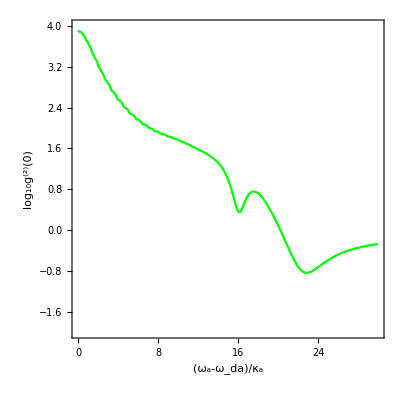

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];
(*定义基本量*)
n=6;(*定义光场展开数*)
columnlengthcavity=n;
columnlengthatom=32;(*原子基矢数*)
columnlengthf=columnlengthcavity*columnlengthatom;
columncut=8;
matrixvariablef=columncut*columncut;(*ρf的变元数*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
σr={{0,1},{0,0}};
σl={{0,0},{1,0}};
unity2={{1,0},{0,1}};
unityatom=IdentityMatrix[columnlengthatom];
unitycavity=IdentityMatrix[n];
(*定义光子数空间在基矢0，1，2,3,4,5下算符的矩阵表示*)
a={{0,1,0,0,0,0},{0,0,√2,0,0,0},{0,0,0,√3,0,0},{0,0,0,0,2,0},{0,0,0,0,0,√5},{0,0,0,0,0,0}};
adaige={{0,0,0,0,0,0},{1,0,0,0,0,0},{0,√2,0,0,0,0},{0,0,√3,0,0,0},{0,0,0,2,0,0},{0,0,0,0,√5,0}};
(*定义全空间ee0,eg0,ge0,gg0,gg1,ee2,eg2,ge2,gg2算符的矩阵表示，变量名都加f表示*)
af=KroneckerProduct[a,unityatom];
adaigef=KroneckerProduct[adaige,unityatom];
σx1f=KroneckerProduct[unitycavity,σx,unity2,unity2,unity2,unity2];
σz1f=KroneckerProduct[unitycavity,σz,unity2,unity2,unity2,unity2];
σr1f=KroneckerProduct[unitycavity,σr,unity2,unity2,unity2,unity2];
σl1f=KroneckerProduct[unitycavity,σl,unity2,unity2,unity2,unity2];
σx2f=KroneckerProduct[unitycavity,unity2,σx,unity2,unity2,unity2];
σz2f=KroneckerProduct[unitycavity,unity2,σz,unity2,unity2,unity2];
σr2f=KroneckerProduct[unitycavity,unity2,σr,unity2,unity2,unity2];
σl2f=KroneckerProduct[unitycavity,unity2,σl,unity2,unity2,unity2];
σx3f=KroneckerProduct[unitycavity,unity2,unity2,σx,unity2,unity2];
σz3f=KroneckerProduct[unitycavity,unity2,unity2,σz,unity2,unity2];
σr3f=KroneckerProduct[unitycavity,unity2,unity2,σr,unity2,unity2];
σl3f=KroneckerProduct[unitycavity,unity2,unity2,σl,unity2,unity2];
σx4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σx,unity2];
σz4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σz,unity2];
σr4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σr,unity2];
σl4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σl,unity2];
σx5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σx];
σz5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σz];
σr5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σr];
σl5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σl];
Jlf=σl1f+σl2f+σl3f+σl4f+σl5f;
Jrf=σr1f+σr2f+σr3f+σr4f+σr5f;
Jxf=Jlf+Jrf;
ρeeggg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρegegg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρeggeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρeggge0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];
ρgeegg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρgegeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρgegge0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];
ρggeeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρggege0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];
ρgggee0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];


(*设定参数*)
ωr=8*2*Pi;
ωq=8*2*Pi;

g=ratio*ωr;
ratio=0.01;
Δ=0.4*ωr;
γ=0.1*g;
κ=0.1*g;

E1=3*κ;
t0=200;

(*主方程的右边*)
H=ωq/2*σz1f+ωq/2*σz2f+ωq/2*σz3f+ωq/2*σz4f+ωq/2*σz5f+ωr*adaigef.af+Δ*(ρeeggg0+ρegegg0+ρeggeg0+ρeggge0+ρgeegg0+ρgegeg0+ρgegge0+ρggeeg0+ρggege0+ρgggee0)+g*(adaigef.(σl1f)+af.(σr1f))+g*(adaigef.(σl2f)+af.(σr2f))+g*(adaigef.(σl3f)+af.(σr3f))+g*(adaigef.(σl4f)+af.(σr4f))+g*(adaigef.(σl5f)+af.(σr5f));                
  (*write in the Schrödinger picture, can be further examined by  PRA  Multiphoton Quantum Rabi Oscillations*)
dataEigen=Chop[Eigensystem[H]];
dataEigensorted=Sort[Table[{dataEigen[[1,m]],dataEigen[[2,m]]},{m,columnlengthf}],#1[[1]]<#2[[1]]&];
(*sorted with eigenvalue from small to large. Table!*)
SToH=Table[dataEigensorted[[m,2]],{m,columnlengthf}];  
(*行向量排列的变换矩阵S*)



Hcut=Take[SToH.H.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
afcut=Take[SToH.af.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
adaigefcut=Take[SToH.adaigef.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl1fcut=Take[SToH.σl1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr1fcut=Take[SToH.σr1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl2fcut=Take[SToH.σl2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr2fcut=Take[SToH.σr2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl3fcut=Take[SToH.σl3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr3fcut=Take[SToH.σr3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl4fcut=Take[SToH.σl4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr4fcut=Take[SToH.σr4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl5fcut=Take[SToH.σl5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr5fcut=Take[SToH.σr5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
(*定义全空间密度矩阵变量*)
ρf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρf[[i,j]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[t]"]]
]
];
(*生成初值*)
ρinitialatom=KroneckerProduct[({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];(*初始是 1/4(（++++）+（+++-）+（++-+）+...+（----）)*)
vinitialcavity=({{1}, {0}, {0}, {0}, {0}, {0}});
ρinitialcavity=vinitialcavity.ConjugateTranspose[vinitialcavity];
ρinitialf=Take[SToH.ArrayFlatten[Outer[Times,ρinitialcavity, ρinitialatom]].ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
DistributeDefinitions[ρinitialf,ρf,σr5fcut,σl5fcut,σr4fcut,σl4fcut,σr3fcut,σl3fcut,σr2fcut,σl2fcut,σr1fcut,σl1fcut,adaigefcut,afcut,Hcut,t0,g,E1,κ,γ,ωr,matrixvariablef,columncut];
data=ParallelTable[
ωd=ωr-m*κ;
H1cut=Hcut+E1*Cos[ωd*t]*(adaigefcut+afcut); 


(*主方程的右边*)
i=.;
j=.;
rightmasterequa=I*(ρf.H1cut-H1cut.ρf)+κ/2*(2*afcut.ρf.adaigefcut-ρf.adaigefcut.afcut-adaigefcut.afcut.ρf)+γ/2*(2*σl1fcut.ρf.σr1fcut-ρf.σr1fcut.σl1fcut-σr1fcut.σl1fcut.ρf)+γ/2*(2*σl2fcut.ρf.σr2fcut-ρf.σr2fcut.σl2fcut-σr2fcut.σl2fcut.ρf)+γ/2*(2*σl3fcut.ρf.σr3fcut-ρf.σr3fcut.σl3fcut-σr3fcut.σl3fcut.ρf)+γ/2*(2*σl4fcut.ρf.σr4fcut-ρf.σr4fcut.σl4fcut-σr4fcut.σl4fcut.ρf)+γ/2*(2*σl5fcut.ρf.σr5fcut-ρf.σr5fcut.σl5fcut-σr5fcut.σl5fcut.ρf);
(*生成方程组和初值*)
equ=Table[0,{matrixvariablef*2}];
(*生成方程组*)
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[((i-1)*columncut+j)]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"'","[t]"]]==rightmasterequa[[i,j]]
]
];

For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[matrixvariablef+(((i-1)*columncut+j))]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[0]"]]==ρinitialf[[i,j]]
]
];

(*产生变量数组*)
equvariable=Table[0,{matrixvariablef}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equvariable[[((i-1)*columncut+j)]]=ρf[[i,j]]
]
];
S=NDSolve[equ,equvariable,{t,0,t0},MaxSteps->10000000,Method->{"EquationSimplification"->"Solve"}];
ρsolutionf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρsolutionf[[i,j]]=ρf[[i,j]]/.S[[1,((i-1)*columncut+j)]]
]
];

G20=Tr[adaigefcut.adaigefcut.afcut.afcut.ρsolutionf]/((Abs[Tr[adaigefcut.afcut.ρsolutionf]])^2);
logg20=Mean[Table[Log10[Abs[G20]],{t,t0-1,t0,0.1}]];
{m,logg20},{m,0,30,0.1}];



ListPlot[data,FrameLabel->{"(ω_a-ω_da)/κ_a","log_10g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->True,PlotStyle->{Green},Frame->True,PlotRange->{{0,30},{-2,4}},AspectRatio->1]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

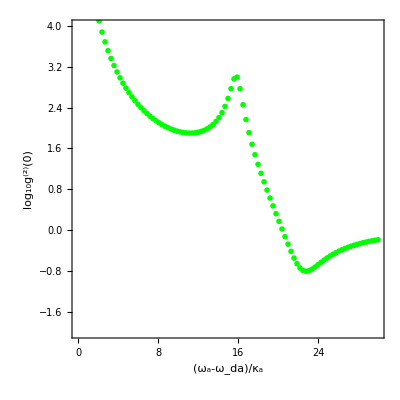

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=8*2*Pi;
ωge=8*2*Pi;


g=0.01*ωr;
γeg=0.1*g;
κ=0.1*g;

F=1.5*κ;
max1=30*κ;
min1=0;      (*max and min value of Δ*)
segment1=100;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
Na=5;
C1=√((4*F^2*Δ^2)/(8*F^4+4 (Na*g^2-Δ^2)^2+8*F^2*(Na*g^2+Δ^2)+Δ^2 κ^2));


equs=Table[{Δ*ToExpression[StringJoin["Ce1",ToString[i]]]+C2*√2*g-I/2*κ*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce1",ToString[i]]]+F*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce1",ToString[i]]]==0,g*C1+F*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce0",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,2*Δ*C2+F*C1*√2-I*κ*C2+g*(Sum[ToExpression[StringJoin["Ce1",ToString[i]]],{i,Na}])*√2==0];


vars={C2,Table[ToExpression[StringJoin["Ce1",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["Ce0",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
Ce1data=Table[ToExpression[StringJoin["Ce1",ToString[i]]]/.S[[1,i+1]],{i,1,Na}];

logg20=Chop[Log10[2/(C1*Conjugate[C1])*(C2data/C1)*(Conjugate[C2data]/Conjugate[C1])]];


{Δ/κ,logg20},{m,1,100+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_a-ω_da)/κ_a","log_10g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->False,PlotStyle->{Green},Frame->True,PlotMarkers->"OpenMarkers",PlotRange->{{0,30},{-2,4}},AspectRatio->1]
```

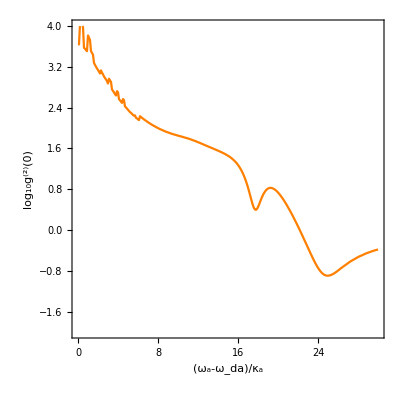

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];
(*定义基本量*)
n=6;(*定义光场展开数*)
columnlengthcavity=n;
columnlengthatom=64;(*原子基矢数*)
columnlengthf=columnlengthcavity*columnlengthatom;
columncut=9;
matrixvariablef=columncut*columncut;(*ρf的变元数*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
σr={{0,1},{0,0}};
σl={{0,0},{1,0}};
unity2={{1,0},{0,1}};
unityatom=IdentityMatrix[columnlengthatom];
unitycavity=IdentityMatrix[n];
(*定义光子数空间在基矢0，1，2,3,4,5下算符的矩阵表示*)
a={{0,1,0,0,0,0},{0,0,√2,0,0,0},{0,0,0,√3,0,0},{0,0,0,0,2,0},{0,0,0,0,0,√5},{0,0,0,0,0,0}};
adaige={{0,0,0,0,0,0},{1,0,0,0,0,0},{0,√2,0,0,0,0},{0,0,√3,0,0,0},{0,0,0,2,0,0},{0,0,0,0,√5,0}};
(*定义全空间ee0,eg0,ge0,gg0,gg1,ee2,eg2,ge2,gg2算符的矩阵表示，变量名都加f表示*)
af=KroneckerProduct[a,unityatom];
adaigef=KroneckerProduct[adaige,unityatom];
σx1f=KroneckerProduct[unitycavity,σx,unity2,unity2,unity2,unity2,unity2];
σz1f=KroneckerProduct[unitycavity,σz,unity2,unity2,unity2,unity2,unity2];
σr1f=KroneckerProduct[unitycavity,σr,unity2,unity2,unity2,unity2,unity2];
σl1f=KroneckerProduct[unitycavity,σl,unity2,unity2,unity2,unity2,unity2];
σx2f=KroneckerProduct[unitycavity,unity2,σx,unity2,unity2,unity2,unity2];
σz2f=KroneckerProduct[unitycavity,unity2,σz,unity2,unity2,unity2,unity2];
σr2f=KroneckerProduct[unitycavity,unity2,σr,unity2,unity2,unity2,unity2];
σl2f=KroneckerProduct[unitycavity,unity2,σl,unity2,unity2,unity2,unity2];
σx3f=KroneckerProduct[unitycavity,unity2,unity2,σx,unity2,unity2,unity2];
σz3f=KroneckerProduct[unitycavity,unity2,unity2,σz,unity2,unity2,unity2];
σr3f=KroneckerProduct[unitycavity,unity2,unity2,σr,unity2,unity2,unity2];
σl3f=KroneckerProduct[unitycavity,unity2,unity2,σl,unity2,unity2,unity2];
σx4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σx,unity2,unity2];
σz4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σz,unity2,unity2];
σr4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σr,unity2,unity2];
σl4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σl,unity2,unity2];
σx5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σx,unity2];
σz5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σz,unity2];
σr5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σr,unity2];
σl5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σl,unity2];
σx6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σx];
σz6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σz];
σr6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σr];
σl6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σl];
Jlf=σl1f+σl2f+σl3f+σl4f+σl5f+σl6f;
Jrf=σr1f+σr2f+σr3f+σr4f+σr5f+σr6f;
Jxf=Jlf+Jrf;
ρeegggg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρegeggg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρeggegg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρegggeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρegggge0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];
ρgeeggg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρgegegg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρgeggeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρgeggge0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];
ρggeegg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρggegeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρggegge0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];
ρgggeeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρgggege0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];
ρggggee0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];


(*设定参数*)
ωr=8*2*Pi;
ωq=8*2*Pi;

g=ratio*ωr;
ratio=0.01;
Δ=0.4*ωr;
γ=0.1*g;
κ=0.1*g;

E1=3*κ;
t0=200;

(*主方程的右边*)
H=ωq/2*σz1f+ωq/2*σz2f+ωq/2*σz3f+ωq/2*σz4f+ωq/2*σz5f+ωq/2*σz6f+ωr*adaigef.af+Δ*(ρeegggg0+ρegeggg0+ρeggegg0+ρegggeg0+ρegggge0+ρgeeggg0+ρgegegg0+ρgeggeg0+ρgeggge0+ρggeegg0+ρggegeg0+ρggegge0+ρgggeeg0+ρgggege0+ρggggee0)+g*(adaigef.(σl1f)+af.(σr1f))+g*(adaigef.(σl2f)+af.(σr2f))+g*(adaigef.(σl3f)+af.(σr3f))+g*(adaigef.(σl4f)+af.(σr4f))+g*(adaigef.(σl5f)+af.(σr5f))+g*(adaigef.(σl6f)+af.(σr6f));                
  (*write in the Schrödinger picture, can be further examined by  PRA  Multiphoton Quantum Rabi Oscillations*)
dataEigen=Chop[Eigensystem[H]];
dataEigensorted=Sort[Table[{dataEigen[[1,m]],dataEigen[[2,m]]},{m,columnlengthf}],#1[[1]]<#2[[1]]&];
(*sorted with eigenvalue from small to large. Table!*)
SToH=Table[dataEigensorted[[m,2]],{m,columnlengthf}];  
(*行向量排列的变换矩阵S*)



Hcut=Take[SToH.H.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
afcut=Take[SToH.af.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
adaigefcut=Take[SToH.adaigef.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl1fcut=Take[SToH.σl1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr1fcut=Take[SToH.σr1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl2fcut=Take[SToH.σl2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr2fcut=Take[SToH.σr2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl3fcut=Take[SToH.σl3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr3fcut=Take[SToH.σr3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl4fcut=Take[SToH.σl4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr4fcut=Take[SToH.σr4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl5fcut=Take[SToH.σl5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr5fcut=Take[SToH.σr5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl6fcut=Take[SToH.σl6f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr6fcut=Take[SToH.σr6f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
(*定义全空间密度矩阵变量*)
ρf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρf[[i,j]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[t]"]]
]
];
(*生成初值*)
ρinitialatom=KroneckerProduct[({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];(*初始是 1/4(（++++）+（+++-）+（++-+）+...+（----）)*)
vinitialcavity=({{1}, {0}, {0}, {0}, {0}, {0}});
ρinitialcavity=vinitialcavity.ConjugateTranspose[vinitialcavity];
ρinitialf=Take[SToH.ArrayFlatten[Outer[Times,ρinitialcavity, ρinitialatom]].ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
DistributeDefinitions[ρinitialf,ρf,σr6fcut,σl6fcut,σr5fcut,σl5fcut,σr4fcut,σl4fcut,σr3fcut,σl3fcut,σr2fcut,σl2fcut,σr1fcut,σl1fcut,adaigefcut,afcut,Hcut,t0,g,E1,κ,γ,ωr,matrixvariablef,columncut];
data=ParallelTable[
ωd=ωr-m*κ;
H1cut=Hcut+E1*Cos[ωd*t]*(adaigefcut+afcut); 


(*主方程的右边*)
i=.;
j=.;
rightmasterequa=I*(ρf.H1cut-H1cut.ρf)+κ/2*(2*afcut.ρf.adaigefcut-ρf.adaigefcut.afcut-adaigefcut.afcut.ρf)+γ/2*(2*σl1fcut.ρf.σr1fcut-ρf.σr1fcut.σl1fcut-σr1fcut.σl1fcut.ρf)+γ/2*(2*σl2fcut.ρf.σr2fcut-ρf.σr2fcut.σl2fcut-σr2fcut.σl2fcut.ρf)+γ/2*(2*σl3fcut.ρf.σr3fcut-ρf.σr3fcut.σl3fcut-σr3fcut.σl3fcut.ρf)+γ/2*(2*σl4fcut.ρf.σr4fcut-ρf.σr4fcut.σl4fcut-σr4fcut.σl4fcut.ρf)+γ/2*(2*σl5fcut.ρf.σr5fcut-ρf.σr5fcut.σl5fcut-σr5fcut.σl5fcut.ρf)+γ/2*(2*σl6fcut.ρf.σr6fcut-ρf.σr6fcut.σl6fcut-σr6fcut.σl6fcut.ρf);
(*生成方程组和初值*)
equ=Table[0,{matrixvariablef*2}];
(*生成方程组*)
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[((i-1)*columncut+j)]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"'","[t]"]]==rightmasterequa[[i,j]]
]
];

For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[matrixvariablef+(((i-1)*columncut+j))]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[0]"]]==ρinitialf[[i,j]]
]
];

(*产生变量数组*)
equvariable=Table[0,{matrixvariablef}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equvariable[[((i-1)*columncut+j)]]=ρf[[i,j]]
]
];
S=NDSolve[equ,equvariable,{t,0,t0},MaxSteps->10000000,Method->{"EquationSimplification"->"Solve"}];
ρsolutionf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρsolutionf[[i,j]]=ρf[[i,j]]/.S[[1,((i-1)*columncut+j)]]
]
];

G20=Tr[adaigefcut.adaigefcut.afcut.afcut.ρsolutionf]/((Abs[Tr[adaigefcut.afcut.ρsolutionf]])^2);
logg20=Mean[Table[Log10[Abs[G20]],{t,t0-20,t0,0.1}]];
{m,logg20},{m,0,30,0.1}];



ListPlot[data,FrameLabel->{"(ω_a-ω_da)/κ_a","log_10g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->True,PlotStyle->{Orange},Frame->True,PlotRange->{{0,30},{-2,4}},AspectRatio->1]
```

```mathematica
data
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

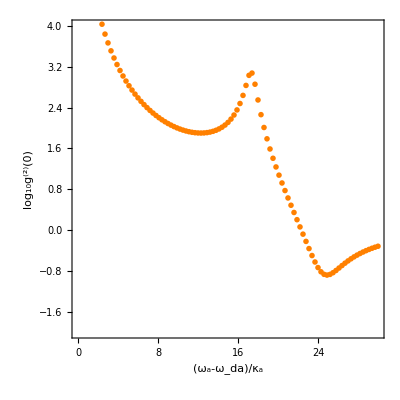

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=8*2*Pi;
ωge=8*2*Pi;


g=0.01*ωr;
γeg=0.1*g;
κ=0.1*g;

F=1.5*κ;
max1=30*κ;
min1=0;      (*max and min value of Δ*)
segment1=100;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
Na=6;
C1=√((4*F^2*Δ^2)/(8*F^4+4 (Na*g^2-Δ^2)^2+8*F^2*(Na*g^2+Δ^2)+Δ^2 κ^2));


equs=Table[{Δ*ToExpression[StringJoin["Ce1",ToString[i]]]+C2*√2*g-I/2*κ*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce1",ToString[i]]]+F*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce1",ToString[i]]]==0,g*C1+F*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce0",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,2*Δ*C2+F*C1*√2-I*κ*C2+g*(Sum[ToExpression[StringJoin["Ce1",ToString[i]]],{i,Na}])*√2==0];


vars={C2,Table[ToExpression[StringJoin["Ce1",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["Ce0",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
Ce1data=Table[ToExpression[StringJoin["Ce1",ToString[i]]]/.S[[1,i+1]],{i,1,Na}];

logg20=Chop[Log10[2/(C1*Conjugate[C1])*(C2data/C1)*(Conjugate[C2data]/Conjugate[C1])]];


{Δ/κ,logg20},{m,1,100+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_a-ω_da)/κ_a","log_10g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->False,PlotStyle->{Orange},Frame->True,PlotMarkers->"OpenMarkers",PlotRange->{{0,30},{-2,4}},AspectRatio->1]
```

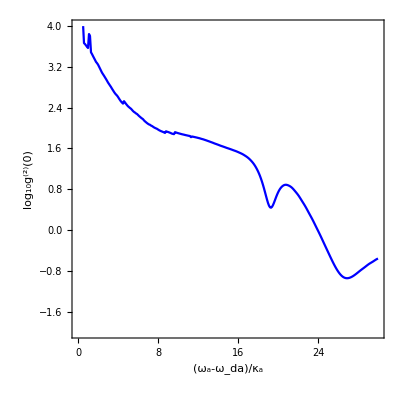

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];
(*定义基本量*)
n=6;(*定义光场展开数*)
columnlengthcavity=n;
columnlengthatom=128;(*原子基矢数*)
columnlengthf=columnlengthcavity*columnlengthatom;
columncut=10;
matrixvariablef=columncut*columncut;(*ρf的变元数*)
σx={{0,1},{1,0}};
σy={{0,-I},{I,0}};
σz={{1,0},{0,-1}};
σr={{0,1},{0,0}};
σl={{0,0},{1,0}};
unity2={{1,0},{0,1}};
unityatom=IdentityMatrix[columnlengthatom];
unitycavity=IdentityMatrix[n];
(*定义光子数空间在基矢0，1，2,3,4,5下算符的矩阵表示*)
a={{0,1,0,0,0,0},{0,0,√2,0,0,0},{0,0,0,√3,0,0},{0,0,0,0,2,0},{0,0,0,0,0,√5},{0,0,0,0,0,0}};
adaige={{0,0,0,0,0,0},{1,0,0,0,0,0},{0,√2,0,0,0,0},{0,0,√3,0,0,0},{0,0,0,2,0,0},{0,0,0,0,√5,0}};
(*定义全空间ee0,eg0,ge0,gg0,gg1,ee2,eg2,ge2,gg2算符的矩阵表示，变量名都加f表示*)
af=KroneckerProduct[a,unityatom];
adaigef=KroneckerProduct[adaige,unityatom];
σx1f=KroneckerProduct[unitycavity,σx,unity2,unity2,unity2,unity2,unity2,unity2];
σz1f=KroneckerProduct[unitycavity,σz,unity2,unity2,unity2,unity2,unity2,unity2];
σr1f=KroneckerProduct[unitycavity,σr,unity2,unity2,unity2,unity2,unity2,unity2];
σl1f=KroneckerProduct[unitycavity,σl,unity2,unity2,unity2,unity2,unity2,unity2];
σx2f=KroneckerProduct[unitycavity,unity2,σx,unity2,unity2,unity2,unity2,unity2];
σz2f=KroneckerProduct[unitycavity,unity2,σz,unity2,unity2,unity2,unity2,unity2];
σr2f=KroneckerProduct[unitycavity,unity2,σr,unity2,unity2,unity2,unity2,unity2];
σl2f=KroneckerProduct[unitycavity,unity2,σl,unity2,unity2,unity2,unity2,unity2];
σx3f=KroneckerProduct[unitycavity,unity2,unity2,σx,unity2,unity2,unity2,unity2];
σz3f=KroneckerProduct[unitycavity,unity2,unity2,σz,unity2,unity2,unity2,unity2];
σr3f=KroneckerProduct[unitycavity,unity2,unity2,σr,unity2,unity2,unity2,unity2];
σl3f=KroneckerProduct[unitycavity,unity2,unity2,σl,unity2,unity2,unity2,unity2];
σx4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σx,unity2,unity2,unity2];
σz4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σz,unity2,unity2,unity2];
σr4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σr,unity2,unity2,unity2];
σl4f=KroneckerProduct[unitycavity,unity2,unity2,unity2,σl,unity2,unity2,unity2];
σx5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σx,unity2,unity2];
σz5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σz,unity2,unity2];
σr5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σr,unity2,unity2];
σl5f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,σl,unity2,unity2];
σx6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σx,unity2];
σz6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σz,unity2];
σr6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σr,unity2];
σl6f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,σl,unity2];
σx7f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,unity2,σx];
σz7f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,unity2,σz];
σr7f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,unity2,σr];
σl7f=KroneckerProduct[unitycavity,unity2,unity2,unity2,unity2,unity2,unity2,σl];
Jlf=σl1f+σl2f+σl3f+σl4f+σl5f+σl6f+σl7f;
Jrf=σr1f+σr2f+σr3f+σr4f+σr5f+σr6f+σr7f;
Jxf=Jlf+Jrf;
ρeeggggg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρegegggg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρeggeggg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρegggegg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρeggggeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρeggggge0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];
ρgeegggg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρgegeggg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρgeggegg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρgegggeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρgegggge0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];
ρggeeggg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρggegegg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρggeggeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρggeggge0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];
ρgggeegg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρgggegeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρgggegge0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];
ρggggeeg0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];
ρggggege0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];
ρgggggee0=KroneckerProduct[({{1}, {0}, {0}, {0}, {0}, {0}}).ConjugateTranspose[({{1}, {0}, {0}, {0}, {0}, {0}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})],({{1}, {0}}).ConjugateTranspose[({{1}, {0}})]];


(*设定参数*)
ωr=8*2*Pi;
ωq=8*2*Pi;

g=ratio*ωr;
ratio=0.01;
Δ=0.4*ωr;
γ=0.1*g;
κ=0.1*g;

E1=3*κ;
t0=200;

(*主方程的右边*)
H=ωq/2*σz1f+ωq/2*σz2f+ωq/2*σz3f+ωq/2*σz4f+ωq/2*σz5f+ωq/2*σz6f+ωq/2*σz7f+ωr*adaigef.af+Δ*(ρeeggggg0+ρegegggg0+ρeggeggg0+ρegggegg0+ρeggggeg0+ρeggggge0+ρgeegggg0+ρgegeggg0+ρgeggegg0+ρgegggeg0+ρgegggge0+ρggeeggg0+ρggegegg0+ρggeggeg0+ρggeggge0+ρgggeegg0+ρgggegeg0+ρgggegge0+ρggggeeg0+ρggggege0+ρgggggee0)+g*(adaigef.(σl1f)+af.(σr1f))+g*(adaigef.(σl2f)+af.(σr2f))+g*(adaigef.(σl3f)+af.(σr3f))+g*(adaigef.(σl4f)+af.(σr4f))+g*(adaigef.(σl5f)+af.(σr5f))+g*(adaigef.(σl6f)+af.(σr6f))+g*(adaigef.(σl7f)+af.(σr7f));                
  (*write in the Schrödinger picture, can be further examined by  PRA  Multiphoton Quantum Rabi Oscillations*)
dataEigen=Chop[Eigensystem[H]];
dataEigensorted=Sort[Table[{dataEigen[[1,m]],dataEigen[[2,m]]},{m,columnlengthf}],#1[[1]]<#2[[1]]&];
(*sorted with eigenvalue from small to large. Table!*)
SToH=Table[dataEigensorted[[m,2]],{m,columnlengthf}];  
(*行向量排列的变换矩阵S*)



Hcut=Take[SToH.H.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
afcut=Take[SToH.af.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
adaigefcut=Take[SToH.adaigef.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl1fcut=Take[SToH.σl1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr1fcut=Take[SToH.σr1f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl2fcut=Take[SToH.σl2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr2fcut=Take[SToH.σr2f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl3fcut=Take[SToH.σl3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr3fcut=Take[SToH.σr3f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl4fcut=Take[SToH.σl4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr4fcut=Take[SToH.σr4f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl5fcut=Take[SToH.σl5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr5fcut=Take[SToH.σr5f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl6fcut=Take[SToH.σl6f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr6fcut=Take[SToH.σr6f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σl7fcut=Take[SToH.σl7f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
σr7fcut=Take[SToH.σr7f.ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
(*定义全空间密度矩阵变量*)
ρf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρf[[i,j]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[t]"]]
]
];
(*生成初值*)
ρinitialatom=KroneckerProduct[({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})],({{0}, {1}}).ConjugateTranspose[({{0}, {1}})]];(*初始是 1/4(（++++）+（+++-）+（++-+）+...+（----）)*)
vinitialcavity=({{1}, {0}, {0}, {0}, {0}, {0}});
ρinitialcavity=vinitialcavity.ConjugateTranspose[vinitialcavity];
ρinitialf=Take[SToH.ArrayFlatten[Outer[Times,ρinitialcavity, ρinitialatom]].ConjugateTranspose[SToH],{1,columncut},{1,columncut}];
DistributeDefinitions[ρinitialf,ρf,σr7fcut,σl7fcut,σr6fcut,σl6fcut,σr5fcut,σl5fcut,σr4fcut,σl4fcut,σr3fcut,σl3fcut,σr2fcut,σl2fcut,σr1fcut,σl1fcut,adaigefcut,afcut,Hcut,t0,g,E1,κ,γ,ωr,matrixvariablef,columncut];
data=ParallelTable[
ωd=ωr-m*κ;
H1cut=Hcut+E1*Cos[ωd*t]*(adaigefcut+afcut); 


(*主方程的右边*)
i=.;
j=.;
rightmasterequa=I*(ρf.H1cut-H1cut.ρf)+κ/2*(2*afcut.ρf.adaigefcut-ρf.adaigefcut.afcut-adaigefcut.afcut.ρf)+γ/2*(2*σl1fcut.ρf.σr1fcut-ρf.σr1fcut.σl1fcut-σr1fcut.σl1fcut.ρf)+γ/2*(2*σl2fcut.ρf.σr2fcut-ρf.σr2fcut.σl2fcut-σr2fcut.σl2fcut.ρf)+γ/2*(2*σl3fcut.ρf.σr3fcut-ρf.σr3fcut.σl3fcut-σr3fcut.σl3fcut.ρf)+γ/2*(2*σl4fcut.ρf.σr4fcut-ρf.σr4fcut.σl4fcut-σr4fcut.σl4fcut.ρf)+γ/2*(2*σl5fcut.ρf.σr5fcut-ρf.σr5fcut.σl5fcut-σr5fcut.σl5fcut.ρf)+γ/2*(2*σl6fcut.ρf.σr6fcut-ρf.σr6fcut.σl6fcut-σr6fcut.σl6fcut.ρf)+γ/2*(2*σl7fcut.ρf.σr7fcut-ρf.σr7fcut.σl7fcut-σr7fcut.σl7fcut.ρf);
(*生成方程组和初值*)
equ=Table[0,{matrixvariablef*2}];
(*生成方程组*)
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[((i-1)*columncut+j)]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"'","[t]"]]==rightmasterequa[[i,j]]
]
];

For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equ[[matrixvariablef+(((i-1)*columncut+j))]]=ToExpression[StringJoin["P",ToString[i],"A",ToString[j],"[0]"]]==ρinitialf[[i,j]]
]
];

(*产生变量数组*)
equvariable=Table[0,{matrixvariablef}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
equvariable[[((i-1)*columncut+j)]]=ρf[[i,j]]
]
];
S=NDSolve[equ,equvariable,{t,0,t0},MaxSteps->10000000,Method->{"EquationSimplification"->"Solve"}];
ρsolutionf=Table[0,{columncut},{columncut}];
For[i=0,i<columncut,i++;
For[j=0,j<columncut,j++;
ρsolutionf[[i,j]]=ρf[[i,j]]/.S[[1,((i-1)*columncut+j)]]
]
];

G20=Tr[adaigefcut.adaigefcut.afcut.afcut.ρsolutionf]/((Abs[Tr[adaigefcut.afcut.ρsolutionf]])^2);
logg20=Mean[Table[Log10[Abs[G20]],{t,t0-10,t0,0.1}]];
{m,logg20},{m,0,30,0.1}];



ListPlot[data,FrameLabel->{"(ω_a-ω_da)/κ_a","log_10g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->True,PlotStyle->{Blue},Frame->True,PlotRange->{{0,30},{-2,4}},AspectRatio->1]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

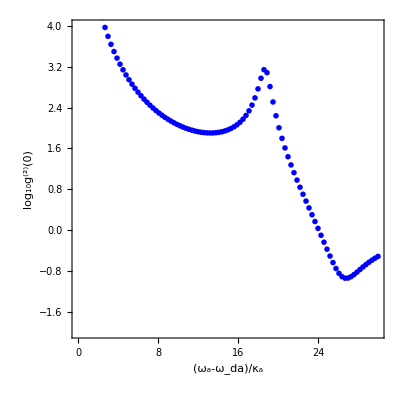

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[62];



data=ParallelTable[
ωr=8*2*Pi;
ωge=8*2*Pi;


g=0.01*ωr;
γeg=0.1*g;
κ=0.1*g;

F=1.5*κ;
max1=30*κ;
min1=0;      (*max and min value of Δ*)
segment1=100;

Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
Na=7;
C1=√((4*F^2*Δ^2)/(8*F^4+4 (Na*g^2-Δ^2)^2+8*F^2*(Na*g^2+Δ^2)+Δ^2 κ^2));


equs=Table[{Δ*ToExpression[StringJoin["Ce1",ToString[i]]]+C2*√2*g-I/2*κ*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce1",ToString[i]]]+F*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce1",ToString[i]]]==0,g*C1+F*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce0",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,2*Δ*C2+F*C1*√2-I*κ*C2+g*(Sum[ToExpression[StringJoin["Ce1",ToString[i]]],{i,Na}])*√2==0];


vars={C2,Table[ToExpression[StringJoin["Ce1",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["Ce0",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
Ce1data=Table[ToExpression[StringJoin["Ce1",ToString[i]]]/.S[[1,i+1]],{i,1,Na}];

logg20=Chop[Log10[2/(C1*Conjugate[C1])*(C2data/C1)*(Conjugate[C2data]/Conjugate[C1])]];


{Δ/κ,logg20},{m,1,100+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


ListPlot[data,FrameLabel->{"(ω_a-ω_da)/κ_a","log_10g^(2)(0)"},BaseStyle->{FontSize->16,FontFamily->"Calibri"},Joined->False,PlotStyle->{Blue},Frame->True,PlotMarkers->"OpenMarkers",PlotRange->{{0,30},{-2,4}},AspectRatio->1]
```

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-]
```